Linfit.nb.  Linear least-squares fit. This fitting program assumes that all data points are weighted equally; i.e., that all points have the same uncertainty.  If you know that different points have different error bars, use the weighted linear fit program Wlinfit.nb.

1/28/13 David Wynne

Enter data points for x and y in the following form: x={x1,x2,...}. Please make sure that there are the same amount of x points are there are y points. To run the entire program at once, press "ctrl + a" and then "shift + enter".
L is the number of data points.

```mathematica
x={0.23931664000000002,0.22014864,0.16744464,0.15936064,0.09560464000000002,0.08952064000000001,0.04376464000000001,0.03968064};
y={1.301669934848,1.2218097921479998,1.009151100672,0.975482820608,0.719177559092,0.6950971434880001,0.49362899153200007,0.48751159411200007};
L=Length[x];
```

```mathematica
ϵ=(Max[x]-Min[x])/10;
δ=(Max[y]-Min[y])/10;
xmin=Min[x]-ϵ;
xmax=Max[x]+ϵ;
ymin=Min[y]-δ;
ymax=Max[y]+δ;
```

Check that your x-y graph looks OK:

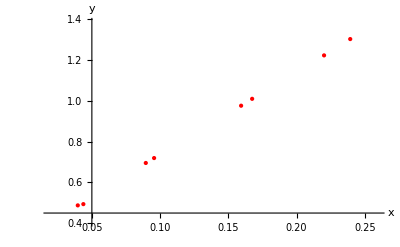

```mathematica
p1=ListPlot[Thread[{x,y}],AxesLabel->{"x","y"},PlotStyle->{Red,PointSize[Large]},PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

```mathematica
Δ=L*∑_(i=1)^L (x[[i]])^2-(∑_(i=1)^L x[[i]])^2
```

0.325834

Δ is a parameter needed for calculations below:

```mathematica
m=1/Δ(L*∑_(i=1)^L (x[[i]]*y[[i]])-(∑_(i=1)^L x[[i]])*∑_(i=1)^L y[[i]])
```

4.09009

m is the slope of the best-fit line.

```mathematica
b=1/Δ((∑_(i=1)^L (x[[i]])^2*∑_(i=1)^L y[[i]])-(∑_(i=1)^L x[[i]])*(∑_(i=1)^L (x[[i]]*y[[i]])))
```

0.323642

b is the intercept of the best-fit line.

```mathematica
σy=√(1/(L-2)*∑_(i=1)^L (y[[i]]-(m*x[[i]]+b))^2)
```

0.00480192

σy is the standard deviation of the difference between the measured y and the predicted y (=mx+b).

```mathematica
δm=√((L*σy^2)/Δ)
```

0.0237937

δm is the uncertainty in the slope

```mathematica
δb=√((σy^2*∑_(i=1)^L (x[[i]])^2)/Δ)
```

0.00356722

Summary:

```mathematica
Grid[{{"m",m},{"δm",δm},{"b",b},{"δb",δb}},Frame->All] (*Run this!*)
```

m | 4.09009
δm | 0.0237937
b | 0.323642
δb | 0.00356722

Check the graph:

```mathematica
f[X_]=m*X+b;
```

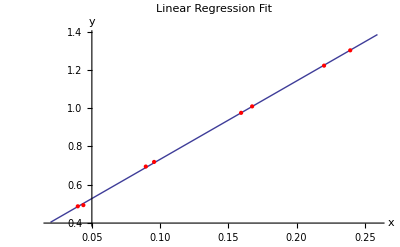

```mathematica
p2=Plot[f[X],{X,xmin,xmax},AxesLabel->{"x","y"},PlotLabel->"Linear Regression Fit"];
Show[p2,p1]
```

```mathematica
Clear[Δ,m,b,δm,δb,p1,p2,σy,x,y]
```

Lookin' good!